## Fractal Dimension of an MRI Tumor Volume Estimated with 3D Box Counting author: Antonio Rueda Toicen antonio.rueda.toicen [at] gmail.com

Each MRI volume has about 15 Mb of data, it’s best to start by clearing global memory.

```mathematica
ClearAll["Global`*"]
```

We set Mathematica’s current directory as this notebook’s directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\CompBio MOOC\Fractal Dimension Tutorial\Box counting CT tutorial

Define local path for datasets

```mathematica
t2Path= "t2.dcm";
groundTruthPath = "truth.dcm";
```

Load brain slices of T2 MRI volume produced by TumorSim

```mathematica
slices = Import[t2Path];
slices = ColorConvert[slices[[1;;160]], "grayscale"];
```

```mathematica
ImageColorSpace[slices[100]]
```

ImageColorSpace[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}[100]]

```mathematica
Manipulate[slices[[i]],{{i,101,"Slice"},1,160,1}]
```

Load ground truth associated to each voxel

```mathematica
groundTruth = Import[groundTruthPath];
groundTruth = ColorConvert[groundTruth[[1;;160]], "grayscale"];
```

```mathematica
groundTruthS = groundTruth;
```

```mathematica
Manipulate[groundTruthS[[i]],{{i,101,"Slice"},1,160,1}]
```

```mathematica
groundTruth = (*Image3D[ColorConvert[groundTruth[[1;;160]],"grayscale"],"Byte"]*)
Image3D[groundTruth, "Byte"]
```

-Graphics3D-

```mathematica
groundTruth = ImageReflect[groundTruth]
```

-Graphics3D-

```mathematica
groundTruth= ImageCrop[groundTruth]
```

-Graphics3D-

Identify the value in the ground truth that labels tumor, we' ll use it to do segmentation

```mathematica
groundTruthS[[101]]
```

-Graphics-

```mathematica
tumorValue=ImageData[-Graphics-][[119,163]];
Print["tumor value is "<>ToString[tumorValue]];

edemaValue = ImageData[-Graphics-][[138,161]];
Print ["edema value is "<>ToString[edemaValue]];
```

Same as this (seen when indexing tumor and edema with image coordinates tool):

```mathematica
tumorValue = 213/255; edemaValue = 170/255;
```

We use the known values of tumor and edema to mark them in the ColorFunction.

```mathematica
Image3D[groundTruth,ColorFunction->(Which[Abs[#-tumorValue]<.1,RGBColor[.9,0,.1,.3],  
		Abs[#-edemaValue]<.1,RGBColor[.8,.5,0,.05],True,RGBColor[0,0,1-#,# .01]]&),
		ViewPoint -> {-3.3816828833769965, -0.10597443501376808, 0.0546835935045555}]

(*tumorValue=0.835294;

edemaValue=0.666667;*)
```

-Graphics3D-

Put all x,y,z coordinates of tumor voxels in a List. Put all x,y,z coordinates of edema voxels in another.

```mathematica
tumorCoordinates = PixelValuePositions[groundTruth, tumorValue];
edemaCoordinates = PixelValuePositions[groundTruth, edemaValue];
```

Cropped volume in Image3D

```mathematica
tumorVolume = ImageCrop[Image3D[SparseArray[Thread[tumorCoordinates->1 ]],
						ColorFunction->(RGBColor[1,0,0,.5#+.01 ]&)]]
```

-Graphics3D-

Edge-detect the tumor volume for box counting.

```mathematica
iEdge = EdgeDetect[tumorVolume]
```

-Graphics3D-

We only need the tumor’s “shell”.

```mathematica
Image3D[iEdge,ClipRange->{{15,45},All,{15,45}}]
```

-Graphics3D-

We’ll use ImagePartition to create boxes.

```mathematica
ImagePartition[iEdge, Floor[Min[ImageDimensions[iEdge]]/4]]
```

{{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}}

3D Box-counting’s function definitions

```mathematica
extractDataFromBoxes[edgeImage_, currentBoxSize_] := 
	Map[ImageData , Flatten[ImagePartition[edgeImage,currentBoxSize]]];

boxCounting[edgeImage_Image3D, 
			initialBoxSize_Integer, 
			maxBoxSize_Integer,boxSizeIncrementStep_Integer ]:=
				
	        ParallelTable[{1/currentBoxSize,Total[ Map [Sign,(Map[Total[#,3]&,
			extractDataFromBoxes[edgeImage, currentBoxSize]])]]},
			{currentBoxSize,initialBoxSize,maxBoxSize,boxSizeIncrementStep}];
```

Specify top box size for measurement

```mathematica
maxBoxSize = Floor[Min[ImageDimensions[iEdge]]/4];
```

Call box counting

```mathematica
logResults = boxCounting[iEdge, 1, maxBoxSize, 1 ]
```

{{1,5266},{1/2,1500},{1/3,710},{1/4,351},{1/5,208},{1/6,135},{1/7,85},{1/8,58},{1/9,52}}

Linear regression to get fractal dimension (as slope)

```mathematica
line=Fit[Log[logResults],{1,x},x]
```

8.75879+2.17341 x

Plot fractal dimension

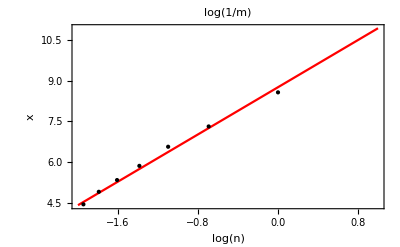

```mathematica
Plot[line,{x,-2,1},Epilog->Point[Log[logResults]],
	 PlotStyle->Red,Frame->True, Axes->True, PlotLabel->Log[1/m],
	 AxesLabel->{Log[n],x},PlotRange->All]
```